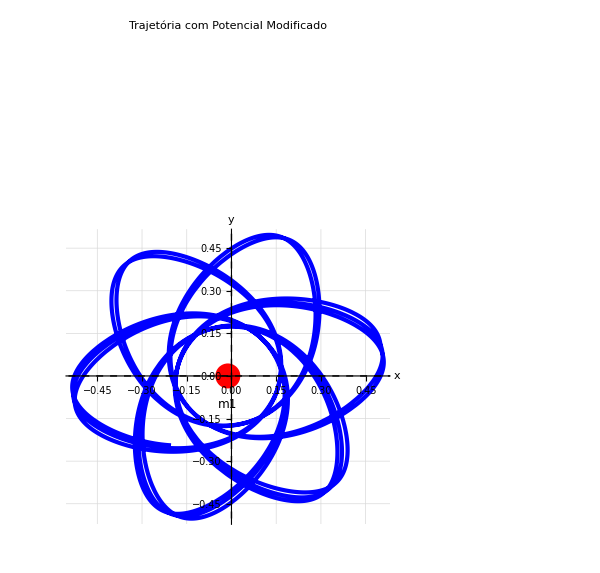

```mathematica
(*Parâmetros adimensionais*)mu=0.01215;       (*Mass ratio*)
beta=0.01;       (*Parâmetro de correção*)

(*Distâncias aos primários*)
r1[x_,y_]:=Sqrt[(x+mu)^2+y^2];
r2[x_,y_]:=Sqrt[(x-(1-mu))^2+y^2];

(*Potencial modificado e forças*)
fx[x_,y_]:=-(1-mu)*(x+mu)/r1[x,y]^3*(1+2*beta/r1[x,y])-mu*(x-(1-mu))/r2[x,y]^3*(1+2*beta/r2[x,y])+x;
fy[x_,y_]:=-(1-mu)*y/r1[x,y]^3*(1+2*beta/r1[x,y])-mu*y/r2[x,y]^3*(1+2*beta/r2[x,y])+y;

(*Equações de movimento*)
eq1=x''[t]==fx[x[t],y[t]]+2*y'[t];
eq2=y''[t]==fy[x[t],y[t]]-2*x'[t];

(*Condições Iniciais*)
(*Condições Iniciais*)
x0=0.5;   (*Posição inicial em x*)
y0=0.1;   (*Posição inicial em y*)
vx0=0.0;  (*Velocidade inicial em x*)
vy0=0.5;  (*Velocidade inicial em y*)

(*Solução numérica*)
sol=NDSolve[{eq1,eq2,x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,20},Method->"StiffnessSwitching",MaxSteps->100000,PrecisionGoal->12,AccuracyGoal->12];

(*Plot da trajetória*)
trajectoryPlot=ParametricPlot[Evaluate[{x[t],y[t]}/. sol],{t,0,20},PlotStyle->{Blue,Thickness[0.005]},PlotRange->All,AxesLabel->{"x","y"},PlotLabel->Style["Trajetória com Potencial Modificado",14,Bold],ImageSize->600,Epilog->{{Red,PointSize[0.03],Point[{-mu,0}],Point[{1-mu,0}]},Text[Style["m1",12],{-mu,-0.1}],Text[Style["m2",12],{1-mu,-0.1}],{Black,Dashed,Line[{{-1.5,0},{1.5,0}}],Line[{{0,-1.5},{0,1.5}}]},Text[Style[StringForm["μ = ``",mu],12],{0.9,1.3}],Text[Style[StringForm["β = ``",beta],12],{0.9,1.1}]},GridLines->Automatic,GridLinesStyle->LightGray];

(*Exibir o gráfico*)
Print[trajectoryPlot];
```

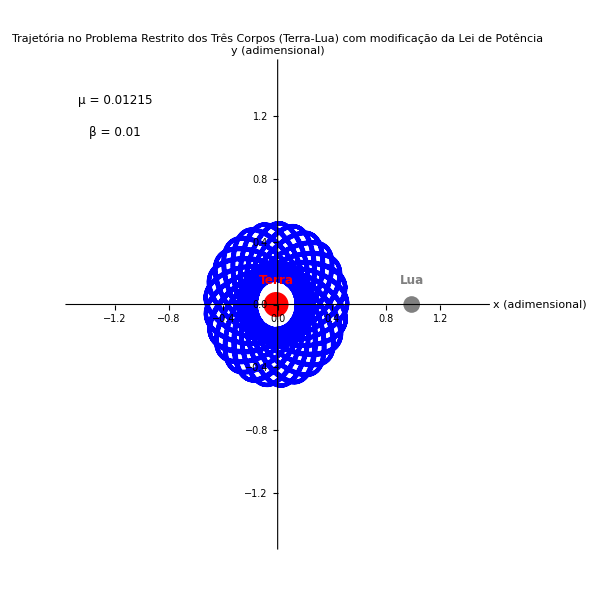

```mathematica
(*Parâmetros do Sistema*)EarthMass=5.97219*10^24;   (*Massa da Terra (kg)*)
MoonMass=7.34767309*10^22;  (*Massa da Lua (kg)*)
mu=MoonMass/(EarthMass+MoonMass); (*Fração de massa da Lua*)
beta=0.01; (*Parâmetro de correção do potencial*)

(*Distâncias adimensionais*)
d1[x_,y_]:=Sqrt[(x+mu)^2+y^2]; (*Distância à Terra*)
d2[x_,y_]:=Sqrt[(x-(1-mu))^2+y^2]; (*Distância à Lua*)

(*Potencial modificado U(x,y) com termo beta*)
U[x_,y_]:=-((1-mu)/d1[x,y]*(1+2*beta/d1[x,y]))-(mu/d2[x,y]*(1+2*beta/d2[x,y]))-(1/2)*(x^2+y^2);

(*Equações do Movimento*)
eq1=x''[t]==-D[U[x[t],y[t]],x[t]]+2*y'[t];
eq2=y''[t]==-D[U[x[t],y[t]],y[t]]-2*x'[t];

(*Condições Iniciais*)
x0=0.5;   (*Posição inicial em x*)
y0=0.1;   (*Posição inicial em y*)
vx0=0.0;  (*Velocidade inicial em x*)
vy0=0.5;  (*Velocidade inicial em y*)

(*Solução Numérica*)
sol=NDSolve[{eq1,eq2,x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,100},Method->"StiffnessSwitching",MaxSteps->100000,PrecisionGoal->12];

(*Plot da Trajetória-SEM GRADE DE LINHAS*)
trajectoryPlot=ParametricPlot[Evaluate[{x[t],y[t]}/. sol],{t,0,100},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},AxesLabel->{"x (adimensional)","y (adimensional)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},PlotLabel->Style["Trajetória no Problema Restrito dos Três Corpos (Terra-Lua)\n com modificação da Lei de Potência",14,Bold],ImageSize->600,Epilog->{{Red,PointSize[0.03],Point[{-mu,0}],Text[Style["Terra",12,Bold],{-mu,0.15}]},{Gray,PointSize[0.02],Point[{1-mu,0}],Text[Style["Lua",12,Bold],{1-mu,0.15}]},Text[Style[StringForm["μ = ``",NumberForm[mu,{4,5}]],12],{-1.2,1.3},Background->White],Text[Style[StringForm["β = ``",beta],12],{-1.2,1.1},Background->White]},GridLines->None]; (*REMOVIDAS AS LINHAS DE GRADE*)

(*Exibir o gráfico*)
Print[trajectoryPlot];
```

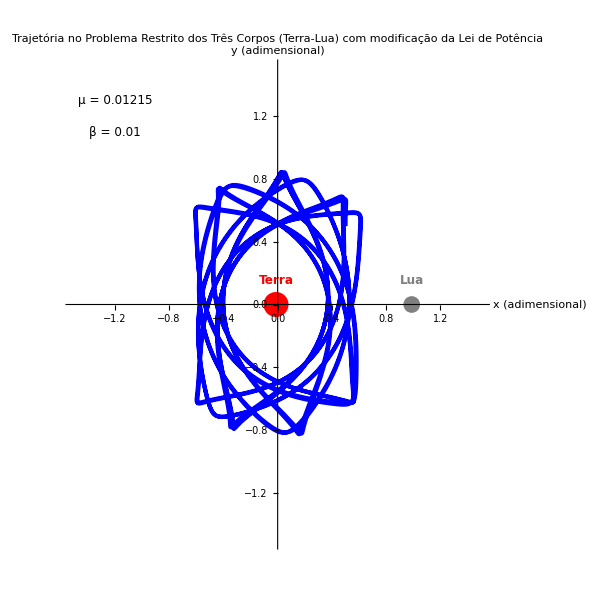

```mathematica
(*Parâmetros do Sistema*)EarthMass=5.97219*10^24;   (*Massa da Terra (kg)*)
MoonMass=7.34767309*10^22;  (*Massa da Lua (kg)*)
mu=MoonMass/(EarthMass+MoonMass); (*Fração de massa da Lua*)
beta=0.01; (*Parâmetro de correção do potencial*)

(*Distâncias adimensionais*)
d1[x_,y_]:=Sqrt[(x+mu)^2+y^2]; (*Distância à Terra*)
d2[x_,y_]:=Sqrt[(x-(1-mu))^2+y^2]; (*Distância à Lua*)

(*Potencial modificado U(x,y) com termo beta*)
U[x_,y_]:=-((1-mu)/d1[x,y]*(1+2*beta/d1[x,y]))-(mu/d2[x,y]*(1+2*beta/d2[x,y]))-(1/2)*(x^2+y^2);

(*Equações do Movimento*)
eq1=x''[t]==-D[U[x[t],y[t]],x[t]]+2*y'[t];
eq2=y''[t]==-D[U[x[t],y[t]],y[t]]-2*x'[t];

(*Condições Iniciais*)
x0=0.5;   (*Posição inicial em x*)
y0=0.5;   (*Posição inicial em y*)
vx0=0.0;  (*Velocidade inicial em x*)
vy0=0.5;  (*Velocidade inicial em y*)

(*Solução Numérica*)
sol=NDSolve[{eq1,eq2,x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,100},Method->"StiffnessSwitching",MaxSteps->100000,PrecisionGoal->12];

(*Plot da Trajetória-SEM GRADE DE LINHAS*)
trajectoryPlot=ParametricPlot[Evaluate[{x[t],y[t]}/. sol],{t,0,100},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},AxesLabel->{"x (adimensional)","y (adimensional)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},PlotLabel->Style["Trajetória no Problema Restrito dos Três Corpos (Terra-Lua)\n com modificação da Lei de Potência",14,Bold],ImageSize->600,Epilog->{{Red,PointSize[0.03],Point[{-mu,0}],Text[Style["Terra",12,Bold],{-mu,0.15}]},{Gray,PointSize[0.02],Point[{1-mu,0}],Text[Style["Lua",12,Bold],{1-mu,0.15}]},Text[Style[StringForm["μ = ``",NumberForm[mu,{4,5}]],12],{-1.2,1.3},Background->White],Text[Style[StringForm["β = ``",beta],12],{-1.2,1.1},Background->White]},GridLines->None]; (*REMOVIDAS AS LINHAS DE GRADE*)

(*Exibir o gráfico*)
Print[trajectoryPlot];
```